```mathematica
Integrate[ x Cos[ n  x], {x, -Pi, Pi}]
```

0

```mathematica
Integrate[ x Sin[ n  x], {x, -Pi, Pi}]
```

(-2 n π Cos[n π]+2 Sin[n π])/n^2

```mathematica
Clear[a, b, x,M, n]
a[n_]:=1/L Integrate[f[x] Cos[(n Pi)/L x], {x, -L, L}]
b[n_]:=1/L Integrate[f[x] Sin[(n Pi)/L x], {x, -L, L}]
F[x_, M_]:= a[0]/2+Sum[a[n] Cos[(n Pi)/L x]+b[n] Sin[(n Pi)/L x],{n, 1, M}]
```

```mathematica
Clear[f, L]
f[x_]:=Abs[x]
L=Pi;
```

```mathematica
Table[a[n], {n, 0, 10}]
```

{π^2,-4,0,-4/9,0,-4/25,0,-4/49,0,-4/81,0}

```mathematica
Table[b[n], {n, 1, 10}]
```

{0,0,0,0,0,0,0,0,0,0}

π/2-(4 Cos[x])/π-(4 Cos[3 x])/(9 π)-(4 Cos[5 x])/(25 π)-(4 Cos[7 x])/(49 π)-(4 Cos[9 x])/(81 π)

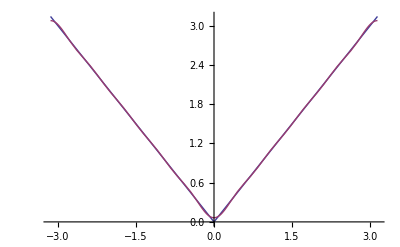

```mathematica
z= Evaluate[F[x, 10]]
Plot[{f[x],z}, {x, -L, L}]
```

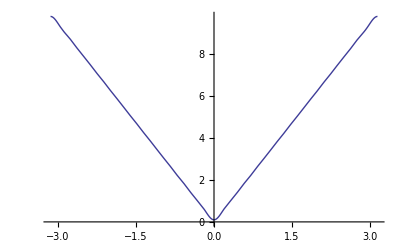

```mathematica
Plot[Evaluate[F[x, 20]], {x, -L, L}]
```

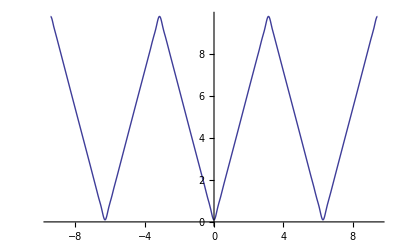

```mathematica
Plot[Evaluate[F[x, 20]], {x, -3L, 3L}]
```

```mathematica
Clear[a, b, x,M,L,  n]
a[n_]:=2/L Integrate[f[x] Cos[(n Pi)/L x], {x, 0, L}]

b[n_]:=2/L Integrate[f[x] Sin[(n Pi)/L x], {x, 0, L}]

FS[x_, M_]:=  Sum[ b[n] Sin[(n Pi)/L x],{n, 1, M}]
FC[x_, M_]:= a[0]/2+Sum[a[n] Cos[(n Pi)/L x] ,{n, 1, M}]
```

```mathematica
Clear[f, L]
f[x_]:=x
L=1
```

1

```mathematica
w=Evaluate[FC[x, 10]]
```

1/2-(4 Cos[π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)-(4 Cos[7 π x])/(49 π^2)-(4 Cos[9 π x])/(81 π^2)

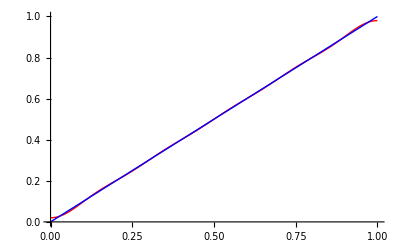

```mathematica
Plot[{w, f[x]}, {x, 0, L},PlotStyle->{Red, Blue}]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)-Sin[6 π x]/(3 π)+(2 Sin[7 π x])/(7 π)-Sin[8 π x]/(4 π)+(2 Sin[9 π x])/(9 π)-Sin[10 π x]/(5 π)+(2 Sin[11 π x])/(11 π)-Sin[12 π x]/(6 π)+(2 Sin[13 π x])/(13 π)-Sin[14 π x]/(7 π)+(2 Sin[15 π x])/(15 π)-Sin[16 π x]/(8 π)+(2 Sin[17 π x])/(17 π)-Sin[18 π x]/(9 π)+(2 Sin[19 π x])/(19 π)-Sin[20 π x]/(10 π)

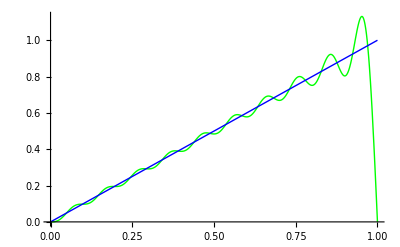

```mathematica
z=Evaluate[FS[x, 20]]
Plot[{ z,f[x]}, {x, 0, L},PlotStyle->{ Green, Blue}]
```

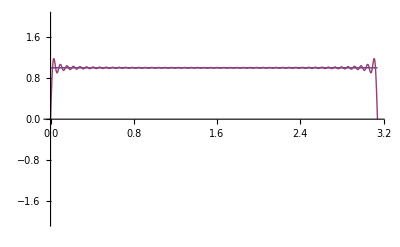

```mathematica
Plot[{f[x], z}, {x, 0, L}, PlotRange->2]
```

### Heat Equation

Number 1

```mathematica
Clear[a, b, x,M,L,  n]
a[n_]:=2/L Integrate[f[x] Cos[(n Pi)/L x], {x, 0, L}]

b[n_]:=2/L Integrate[f[x] Sin[(n Pi)/L x], {x, 0, L}]
```

```mathematica
Clear[f,L]
f[x_]:=x
L=Pi;
```

```mathematica
Table[b[n], {n, 1, 10}]
```

{2,-1,2/3,-1/2,2/5,-1/3,2/7,-1/4,2/9,-1/5}

```mathematica
u[x_,t_, M_]:=Sum[b[n] E^(- k n^2 t)Sin[ n x], {n, 1, M}]
```

```mathematica
k=1;
Plot3D[Evaluate[u[x,t,10]],{x,0, L}, {t, 0, 5}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Evaluate[u[x,t,10]],{x,0, L}, PlotRange->.5], {t, 0, 15}]
```